# “Semi-Inclusive Deep Inelastic Scattering in Wandzura-Wilczek-type approximation” S. Bastami, H. Avakian, A. V. Efremov, A. Kotzinian, B. U. Musch, B. Parsamyan, A. Prokudin, M. Schlegel, G. Schnell, P. Schweitzer, K. Tezgin, W. Vogelsang author : Alexei Prokudin, Kemal Tezgin email : prokudin@jlab.org

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/KML/WW-SIDIS

```mathematica
ExpandFileName["/Users/KML/WW-SIDIS"]
```

/Users/KML/WW-SIDIS

```mathematica
<<wwsidis.m
```

Package WW-SIDIS contains the set of TMDs calculated with WW approximation and SIDIS structure functions

Copyright: Alexei Prokudin (PSU Berks), Kemal Tezgin (UConn), Version 1 (05/21/2018)

e-mail: prokudin@jlab.org

https://github.com/prokudin/WW-SIDIS

___________________________________________________________________________

Contains the following functions:

f1u[x_,Q2_ ] is the unpolarised collinear PDF for u quark

f1d[x_,Q2_ ] is the unpolarised collinear PDF for d quark

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from Grids/mstw2008lo.00.dat

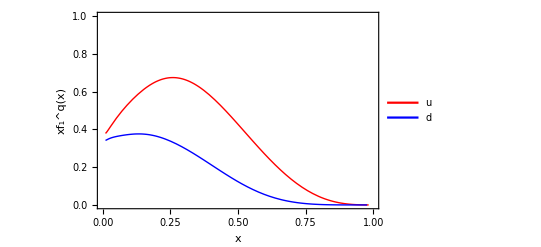

```mathematica
Plot[{x f1u[x,2.4],x f1d[x,2.4]},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{0,1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xf_1^q(x)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

NIntegrate::nlim: wwsidis`Private`y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

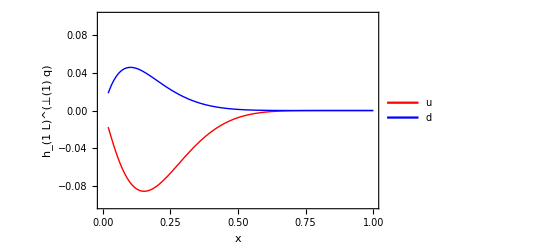

```mathematica
Plot[{h1Lu[x,2.4],h1Ld[x,2.4]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.1,0.1}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","h_(1  L)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d","ū","d̄"},{0.7,0.7}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wwsidis`Private`y near {wwsidis`Private`y} = {0.03031206937143339497087168865618878044188022613525390625}. NIntegrate obtained 6.29799 and 6.90735×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wwsidis`Private`y near {wwsidis`Private`y} = {0.03031206937143339497087168865618878044188022613525390625}. NIntegrate obtained -3.26498 and 8.42643×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wwsidis`Private`y near {wwsidis`Private`y} = {0.0411332}. NIntegrate obtained 0.324507 and 5.45211×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::nlim: wwsidis`Private`y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

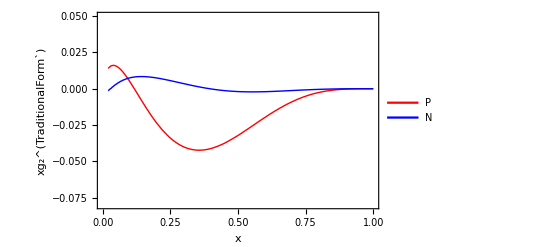

```mathematica
g2plot = Plot[{x*g2[x,7.1],x*g2n[x,7.1]},{x,0.02,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.08,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","xg_2^(TraditionalForm`)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"P","N"},{0.7,0.1}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wwsidis`Private`y near {wwsidis`Private`y} = {0.0204173}. NIntegrate obtained 7.32788 and 0.0000320626 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wwsidis`Private`y near {wwsidis`Private`y} = {0.0204173}. NIntegrate obtained -4.60653 and 0.0000401872 for the integral and error estimates.

NIntegrate::nlim: wwsidis`Private`y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

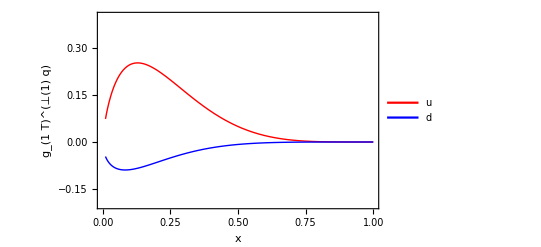

```mathematica
Plot[{g1Tperpu[x,2.4],g1Tperpd[x,2.4](*,g1Tperpubar[x,2.4],g1Tperpdbar[x,2.4]*)},{x,0.01,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.2,0.4}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","g_(1  T)^(⊥(1) q)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"u","d"(*,"ū","d̄"*)},{0.7,0.7}]]
```

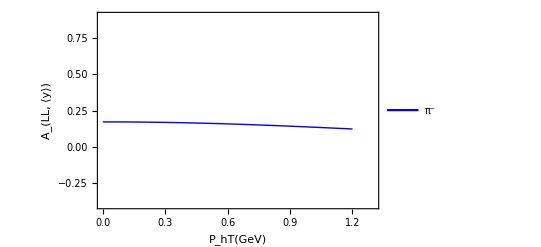

```mathematica
Plot[ALL["pi-",0.257,0.504,1.667,PT],{PT,0,1.2},Frame-> True,PlotRange->{{0,1.3},{-0.4,0.9}}, PlotStyle->{Thick,Blue},FrameLabel->{"P_hT(GeV)","A_(LL, ⟨y⟩)"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^-"},{0.6,0.9}]]
```

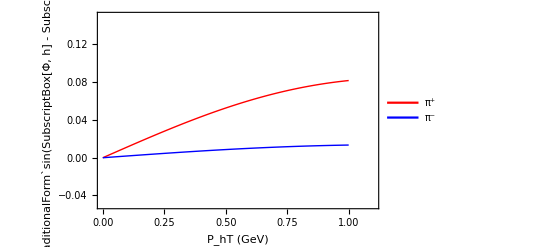

```mathematica
Plot[{AUTSivers["pi+",0.1,0.34,2.4, PT],AUTSivers["pi-",0.1,0.34,2.4, PT]},{PT,0,1.},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.1},{-0.05,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

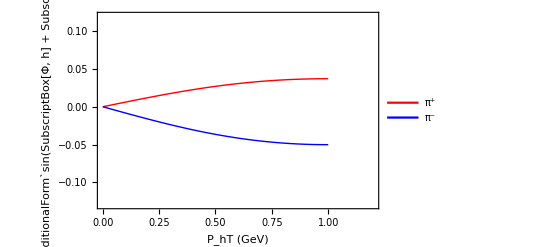

```mathematica
Plot[{AUTCollins["pi+",0.1,0.34,2.4, PT],AUTCollins["pi-",0.1,0.34,2.4, PT]},{PT,0,1.},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1.2},{-0.13,0.12}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(SubscriptBox[Φ, h] + SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

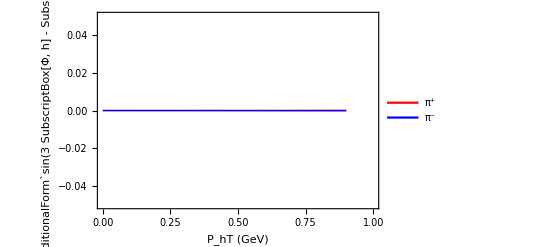

```mathematica
Plot[{AUTh1tp["pi+",0.05,0.35,3.6, PT],AUTh1tp["pi-",0.05,0.35,3.6, PT]},{PT,0,0.9},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT (GeV)","A_UT^(TraditionalForm`sin(3 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

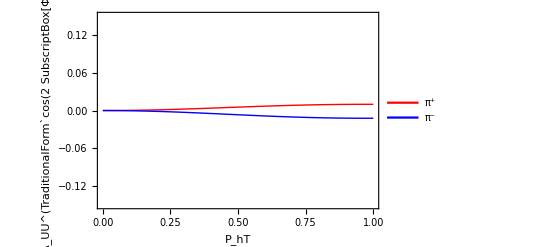

```mathematica
Plot[{AUUcos2phi["pi+",0.1,0.34,2.4,PT],AUUcos2phi["pi-",0.1,0.34,2.4,PT]},{PT,0,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.15,0.15}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT","A_UU^(TraditionalForm`cos(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.1,0.7}]]
```

NIntegrate::nlim: wwsidis`Private`y = x is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

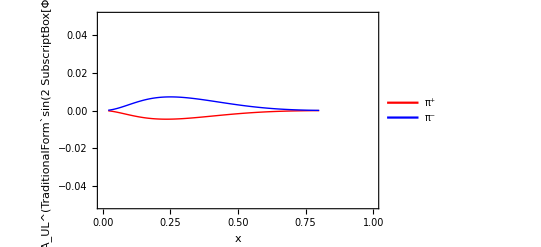

```mathematica
Plot[{AULsin2phiIntegrated["pi+",x,0.36,(2. 160 0.938) 0.05 0.35],AULsin2phiIntegrated["pi-",x,0.36,(2. 160 0.938) 0.05 0.35]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.05,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UL^(TraditionalForm`sin(2 SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.15}]]
```

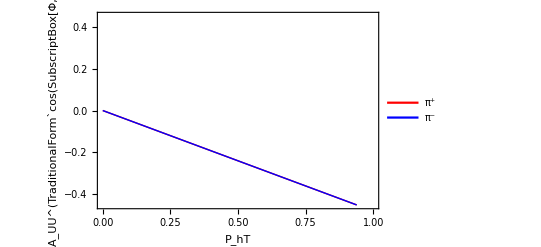

```mathematica
Plot[{AUUcosphi["pi+",0.1,0.34,2.4,PT],AUUcosphi["pi-",0.1,0.34,2.4,PT]},{PT,0,1},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.45,0.45}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"P_hT","A_UU^(TraditionalForm`cos(SubscriptBox[Φ, h]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.1,0.7}]]
```

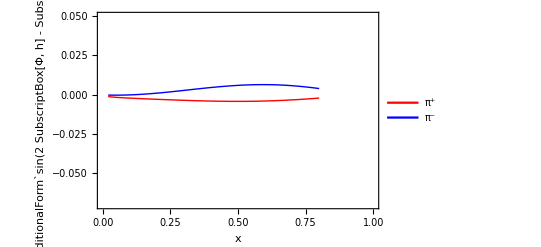

```mathematica
Plot[{AUTsin2PhiminusPhiSIntegrated["pi+",x,0.36,(2. 160 0.938) 0.05 0.35],AUTsin2PhiminusPhiSIntegrated["pi-",x,0.36,(2. 160 0.938) 0.05 0.35]},{x,0.02,0.8},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotRange->{{0,1},{-0.07,0.05}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"x","A_UT^(TraditionalForm`sin(2 SubscriptBox[Φ, h] - SubscriptBox[Φ, S]))"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.7,0.85}]]
```

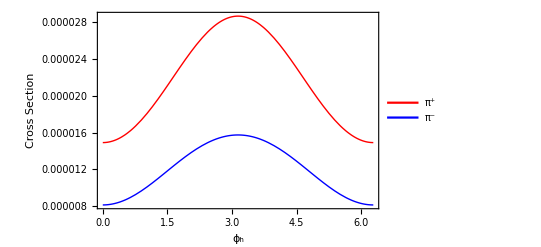

```mathematica
Plot[{CrossSectionUU["pi+",0.3,0.4,2.4,0.5,5.7,phi],CrossSectionUU["pi-",0.3,0.4,2.4,0.5,5.7,phi]},{phi,0,2 Pi},Frame-> True,FrameTicks-> {{Automatic,None},{Automatic,None}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Red,Dashed},{Thick,Blue,Dashed}}, FrameLabel->{"ϕ_h","Cross Section"},BaseStyle->{FontSize->12,FontFamily->"Arial"},PlotLegends->Placed[{"π^+","π^-"},{0.85,0.85}]]
```